# Chapter 47

```mathematica
Total[Table[x*(x+1),{x,1000}]]
```

334334000

```mathematica
Nest[(1/(1+#))&,x,10]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

```mathematica
Flatten@Array[List,{10,10}]
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10}

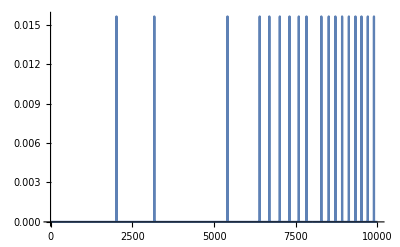

```mathematica
ListLinePlot[Table[First[Timing[n^n]],{n,10000}]]
```

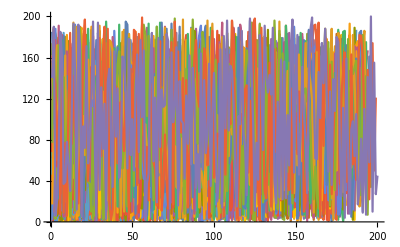

```mathematica
ListLinePlot[First/@Timing@Sort/@Table[RandomSample[Range[n]],{n,200}]]
```

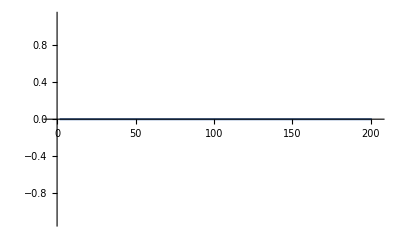

# Chapter 48

```mathematica
Keys@Counts[If[StringLength[#]>1,StringTake[#,2],Nothing]&/@WordList[]]
```

{aa,ab,ac,ad,ae,af,ag,ah,ai,AI,aj,ak,al,am,an,ao,ap,Ap,aq,ar,as,AS,at,au,Au,av,aw,ax,ay,az,ba,BA,be,bi,bl,bo,br,bu,by,ca,ce,ch,ci,cl,cn,co,CO,cr,cu,cy,cz,da,dB,de,De,dh,di,DN,do,DO,dr,du,dw,dy,ea,eb,ec,ed,ee,e',ef,eg,eh,ei,ej,el,em,en,eo,ep,eq,er,es,et,eu,ev,ew,ex,ey,fa,fe,Fe,fi,fj,fl,fo,FO,fr,Fr,fu,ga,ge,gh,gi,gl,gn,go,Go,gr,gu,gy,ha,he,hi,HI,h',hm,ho,hu,hy,ia,ib,ic,id,if,ig,il,im,in,io,ip,IQ,ir,is,it,iv,ja,Ja,je,ji,jo,ju,Ju,ka,kc,ke,kh,kH,ki,kl,kn,ko,kp,kr,ku,kv,kW,la,le,li,ll,lo,lu,ly,ma,Ma,me,mi,mn,mo,Mo,ms,mu,my,na,ne,ni,no,No,nt,nu,ny,oa,ob,oc,o',Oc,od,oe,of,og,oh,oi,ok,ol,om,on,oo,op,or,os,ot,ou,ov,ow,ox,oy,oz,pa,pe,pf,pH,ph,pi,pl,pn,po,pr,ps,pt,pu,py,qu,ra,re,rh,ri,ro,ru,ry,sa,Sa,sc,se,Se,sh,si,sk,sl,sm,sn,so,sp,sq,st,su,Su,sv,sw,sy,ta,te,th,Th,ti,TN,to,tr,ts,tu,Tu,TV,tw,ty,ub,ud,UF,ug,uk,ul,um,un,UN,up,ur,us,ut,uv,ux,va,ve,vi,VI,vo,vu,wa,we,We,wh,wi,wo,wr,xe,xi,xy,ya,ye,yi,yo,yt,yu,za,ze,zi,zl,zo,zu,zw,zy}

```mathematica
Last@Reap@Fold[10 Sow[#1]+#2&,{1,2,3,4,5}]
```

{{1,12,123,1234}}

```mathematica
Last@Reap@Nest[If[EvenQ[#],Sow[#]/2,3#+1]&,1000,20]
```

{{1000,500,250,376,188,94,142,214,322,484,242,364,182}}